### Development Summary

I thought a Mathematica document might be more useful than a pdf. I think there are several reasons to be optimistic about the possibility of applying dispersion kernel techniques to Google’s Flu Trend Data. First and foremost is that google has increased the functionality of their API and doubled the spatial resolution (or at least the number of “advertising regions”). The concern about which search terms to use was taken care of by the addition of the “getTopQueries” method, which for a given query and set of restrictions (spatiotemporal) outputs the most highly correlated queries. Some of these are junk (“george bush” correlates to “Katrina,” but this probably isn’t helpful for finding μ), but others aren’t (“hurricane”, “katrina photos”, etc.). They also appear to have fixed whatever bug was limiting my access to a few hundred queries a day. The second is that google has added a visual interface to their trends API, making it very easy to find potentially interesting events/terms which can be used to extract a μ value. I believe this approach of using several different “events” which spread via the same medium (eg. different natural disaster searches all spread via news and word of mouth) will be useful in pulling the signal (μ of the medium) from the noise (event specific effects + generic randomness). The third is that mathematicas “geo-analysis” methods have become much more powerful. Finally, with several tweaks last semester, the kernel inversion procedure is working very consistently on two dimensional data for the full range of μ values considered, as well as for some non point source simulations (I use a fixed point method to calculate the pair μ,Τ where Τ is the “effective time” at which data collection begins). Hopefully this means it will be able to handle more realistic data like the flu which has no clear source. I’ve given several possible examples below.

Above is a rough picture of what I mean by “effective start time.” I’ll explain the method I’m using to find it geometrically tomorrow. I haven’t labelled my axes in the time series plots below; the vertical is search volume per day (order of one-ten million for the restricted regions and events below).

### Useful Preliminaries

```mathematica
dmas=Import["~/Desktop/BioPhys/flu_project/data_inputs/dmas.csv"][[2;;]];
```

```mathematica
dmadict=Table[dmas[[i]][[1]]->dmas[[i]][[1;;]],{i,1,Length[dmas]}];
```

```mathematica
geoball[dma_,radius_]:=Return@Select[dmas,GeoDistance[GeoPosition[{(dma/.dmadict)[[4]],(dma/.dmadict)[[3]]}],GeoPosition[{#[[4]],#[[3]]}]]<radius LinguisticAssistant&];
```

### “Flu” Search Data from 2005-2015 USA, 1day resolution.

Reasoning: Flu passes from person to person (local transmission) and causes google searches. 
Difficulties: Hard to isolate a source for a specific outbreak.
Top Correlated Searches: Avian Flu, Bird Flu, Flu Symptoms, Dog Flu, Flu Shots. Of these I would say only “flu symptoms” is useful.

```mathematica
fludata =Import["~/Desktop/BioPhys/flu_project/data_outputs/flu_data_2007-01-01_2015-01-01_day_2017-02-1002:34:35.910149.csv"];
For[i=2,i≤Length[fludata],i+=1,
fludata[[i]][[4]]=Map[ToExpression[#]&,StringSplit[StringDrop[StringDrop[fludata[[i]][[4]],1],-1],","]];
];
```

```mathematica
Manipulate[GeoRegionValuePlot[Table[GeoPosition[{fludata[[i]][[2]],fludata[[i]][[3]]}]->fludata[[i]][[4]][[k]],{i,2,Length[fludata]}],ColorFunction->ColorData["TemperatureMap"]],{k,1,Length[fludata[[4]][[4]]]}]
```

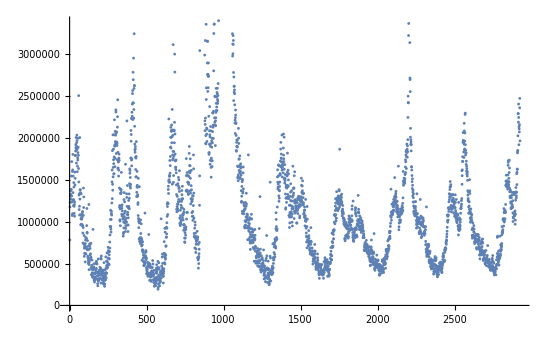

```mathematica
ListPlot[Table[Total@Table[fludata[[i]][[4]][[t]],{i,2,Length[fludata]}],{t,1,Length[fludata[[2]][[4]]]}]]
```

```mathematica
Manipulate[
Grid[{{Text[fludata[[entry]][[1]]/.dmadict]},
{ListPlot[Table[fludata[[entry]][[4]][[k]],{k,1,Length[fludata[[entry]][[4]]]}]]}}],{entry,2,Length[fludata],1}]
```

```mathematica
dmadict[[1]]
```

662→{Abilene-Sweetwater, TX,-99.8294,32.4043}

### “Katrina” Search Data from 8/01/2005 - 12/30/2005. Region within 600 miles of New Orleans.

Reasoning: Well specified event. News travels quickly but perhaps local news and the spread of “fear” and/or “concern” was somehow local (people talking to their friends, family, etc. Said fear/concern would produce google searches. 
Difficulties: Smaller amount of data since it is a single event. Unclear whether “spread of concern” is spatial (the internet is not spatial).
Top Correlated Searches: Hurricane, katrina hurricane, new orleans, hurricane katrina.

```mathematica
katrinadata=Import["~/Desktop/BioPhys/flu_project/data_outputs/katrina_data_2005-08-01_2005-12-30_day_2017-02-1003:16:18.232615.csv"];
For[i=2,i≤Length[katrinadata],i+=1,
katrinadata[[i]][[4]]=Map[ToExpression[#]&,StringSplit[StringDrop[StringDrop[katrinadata[[i]][[4]],1],-1],","]];
];
```

```mathematica
Manipulate[
Grid[{{DateObject["7/31/2005"]+Quantity[1, "Days"]*t},{
GeoRegionValuePlot[Select[Table[GeoPosition[{katrinadata[[i]][[2]],katrinadata[[i]][[3]]}]->katrinadata[[i]][[4]][[t]],{i,2,Length[katrinadata]}],GeoDistance[#[[1]],GeoPosition[Entity["City",{"NewOrleans","Louisiana","UnitedStates"}]]][[1]]<600&],ColorFunction->ColorData["TemperatureMap"]]}}],Row[{Control[{t,1,Length[katrinadata[[4]][[4]]],1}],Spacer[5],"t is in days",Spacer[2]}]]
```

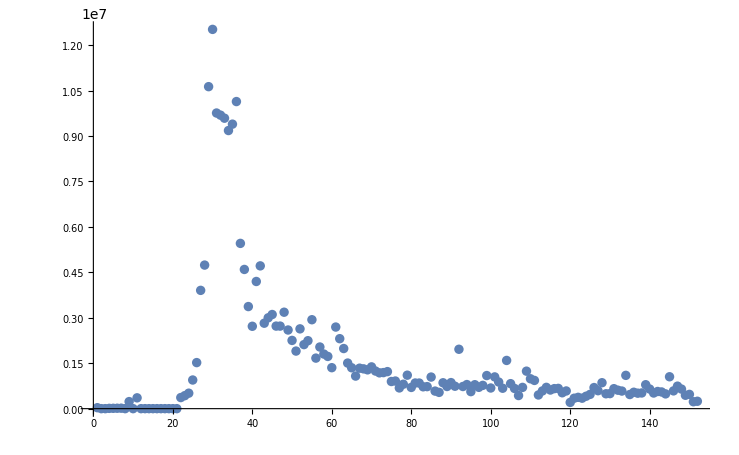

```mathematica
ListPlot[Tooltip[#]&/@Table[Total[Transpose[Select[Table[{GeoPosition[{katrinadata[[i]][[2]],katrinadata[[i]][[3]]}],katrinadata[[i]][[4]][[t]]},{i,2,Length[katrinadata]}],GeoDistance[#[[1]],GeoPosition[Entity["City",{"NewOrleans","Louisiana","UnitedStates"}]]][[1]]<200&]][[2]]],{t,1,Length[katrinadata[[2]][[4]]],1}],PlotRange->All]
```

This ramp up might be too fast for us to resolve spatially; it’s a shame that one wouldn’t expect “lack of concern” to spread like a disease, as it would be much easier to analyze.

### Cicada Search Data from 2/1/2004 - 7/1/2004 USA, 1 day resolution. Region within 1000 miles of DC.

Reasoning: Slower time ramp means it might be easier to resolve this data spatially. In both this case and the Katrina case, the rough geographic “ground zero” is known. Unclear whether this will provide a viable case for kernel extraction, as I think synchronized cicada emergence has more to do with ground temperatures than with some kind of signalling between them. Still, it’s an interesting test case. May 2004 was the largest Cicada resurgence in recent memory.
Difficulties: Synchronization might be forced externally via temperature rather than via local communication
Top Correlated Searches: Locust, Cicada Locust, Cicada Brood, Cicada Maryland

```mathematica
cicadadata=Import["~/Desktop/BioPhys/flu_project/data_outputs/cicada_data_2004-02-01_2004-07-01_day_2017-02-1003:30:06.393409.csv"];
For[i=2,i≤Length[cicadadata],i+=1,
cicadadata[[i]][[4]]=Map[ToExpression[#]&,StringSplit[StringDrop[StringDrop[cicadadata[[i]][[4]],1],-1],","]];
];
```

```mathematica
Manipulate[
Grid[{{DateObject["1/31/2004"]+Quantity[1, "Days"]*t},{
GeoRegionValuePlot[Select[Table[GeoPosition[{cicadadata[[i]][[2]],cicadadata[[i]][[3]]}]->cicadadata[[i]][[4]][[t]],{i,2,Length[cicadadata]}],GeoDistance[#[[1]],GeoPosition[Entity["City",{"Washington","DistrictOfColumbia","UnitedStates"}]]][[1]]<1000&],ColorFunction->ColorData["TemperatureMap"]]}}],Row[{Control[{t,1,Length[cicadadata[[4]][[4]]],1}],Spacer[5],"t is in days",Spacer[2]}]]
```

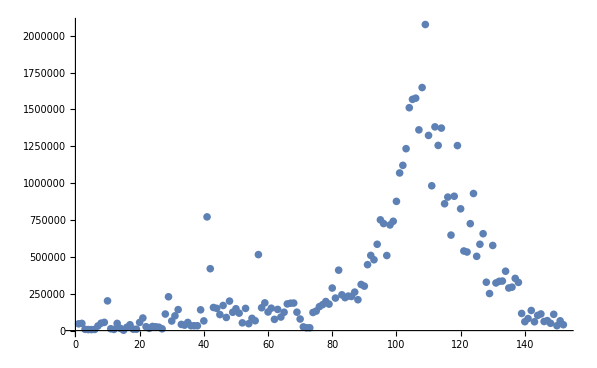

```mathematica
ListPlot[Table[Total[Transpose[Select[Table[{GeoPosition[{cicadadata[[i]][[2]],cicadadata[[i]][[3]]}],cicadadata[[i]][[4]][[t]]},{i,2,Length[cicadadata]}],GeoDistance[#[[1]],GeoPosition[Entity["City",{"Washington","DistrictOfColumbia","UnitedStates"}]]][[1]]<1000&]][[2]]],{t,1,Length[cicadadata[[2]][[4]]],1}],PlotRange->All]
```

### Herpes Search Data from 2005 to 2015, USA, 1 day resolution.

Reasoning: STD’s are an obvious choice for this kind of analysis. They are well tracked, and spread person to person. They also prompt people to search for symptoms/medicines via Google. Unlike the Flu STDs are not seasonal and have (I would guess) I slower propagation rate and larger μ, which provides a different sort of test case. Other options are HIV, etc.
Difficulties: Same as the Flu; no clear origin/source.
Top Correlated Searches: HSV, Herpes Symptoms, Herpes Simplex, Herpes Genital

```mathematica
herpesdata=Import["~/Desktop/BioPhys/flu_project/data_outputs/herpes_data_2005-01-01_2015-01-01_day_2017-02-1006:07:15.342166.csv"];
For[i=2,i≤Length[herpesdata],i+=1,
herpesdata[[i]][[4]]=Map[ToExpression[#]&,StringSplit[StringDrop[StringDrop[herpesdata[[i]][[4]],1],-1],","]];
];
```

```mathematica
Manipulate[GeoRegionValuePlot[Table[GeoPosition[{herpesdata[[i]][[2]],herpesdata[[i]][[3]]}]->herpesdata[[i]][[4]][[k]],{i,2,Length[herpesdata]}],ColorFunction->ColorData["TemperatureMap"]],{k,1,Length[herpesdata[[4]][[4]]]}]
```

GeoRegionValuePlot::reps: {} is not a list of rules of the form loc -> val

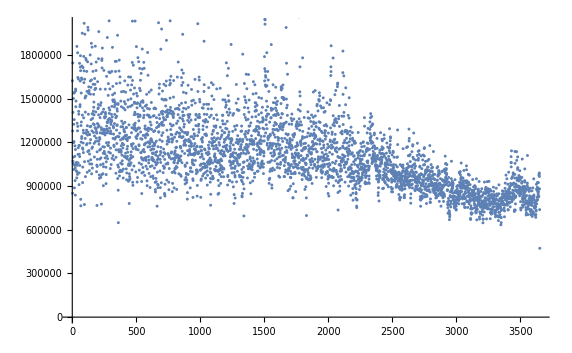

```mathematica
ListPlot[Table[Total@Table[herpesdata[[i]][[4]][[t]],{i,2,Length[herpesdata]}],{t,1,Length[herpesdata[[2]][[4]]]}]]
```

```mathematica
MatrixForm[{{1,2}}]
```

(1 | 2)